# Manipulador Antropomórfico

Longitud de la recta = 31.6228

-Graphics-

-Graphics-

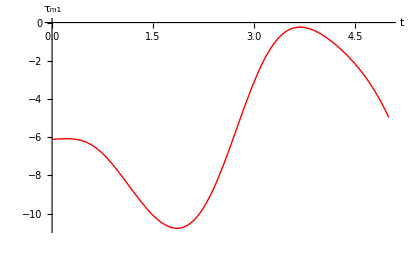

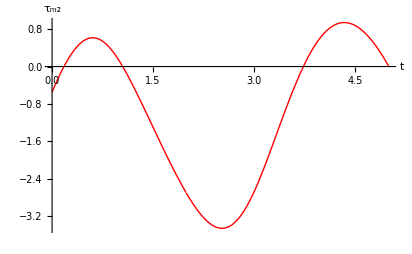

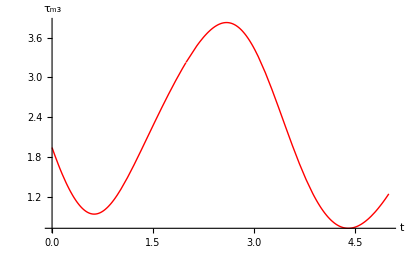

```mathematica
(* Suposición: los eslabones están hecho de MDF *)
(* densidad MDF = 500 [kg/m^3]*)
ρ=500;

(* Aceleración gravitatoria *)
g=-9.81;

(* Datos del eslabón 1 o Cilindro *)
(* Valor de d1/Altura del cilindro *)
d1=15;
(* Radio Cilindro *)
RadCil=2.5;

(* masa del cilindro *)
m[1]=ρ (π (RadCil/100)^2*(d1/100));

(* Datos del eslabón 2 *)
(* Espesor eslabón 2*)
e2=5;
(* Ancho eslabón 2 *)
g2=5;
(* Largo eslabón 2*)
l2=20;

(* masa eslabón 2 *)
m[2]=ρ(e2/100)(g2/100)(l2/100);

(* Datos del eslabón 3 *)
(* Espesor eslabón 3 *)
e3=5;
(* Ancho eslabón 3 *)
g3=5;
(* Largo eslabón 3*)
l3=20;
(* masa eslabón 3 *)
m[3]=ρ(e3/100)(g3/100)(l3/100);


(* Construcción del plano de trabajo *)
NA={-15,30,25};
NB={-15,20,15};
NC={15,20,15};
ND={15,30,25};
plano=Line[{NA,NB,NC,ND,NA}];

(* Construcción de la trayectoria en línea recta *)
Linea=Line[{NA,NC}];

P0=NA;
Pf=NC;


(* Introducción del perfil quíntico *)
(* Longitud de la recta *)
qf=√((Pf[[1]]-P0[[1]])^2+(Pf[[2]]-P0[[2]])^2)//N;
Print["Longitud de la recta = ",qf]

(* Tiempo de operación *)
tf=5;

(* Perfil de trayectoria quíntico *)
q=qf(10(t/tf)^3-15(t/tf)^4+6(t/tf)^5);

(* Parametrizando la recta *)

x=P0[[1]]+q/qf(Pf[[1]]-P0[[1]]);
y=P0[[2]]+q/qf(Pf[[2]]-P0[[2]]);
z=P0[[3]]+q/qf(Pf[[3]]-P0[[3]]);

(* Longitud eslabón 1 *)
l1=d1;

(* l2 y l3 conocidos desde el inicio *)
(* l4, l5, l6, α, β t γ vienen del análisis de la cinemática inversa *)

l4=z-l1;
l5=√(x^2+y^2);
l6=√(l4^2+l5^2);

θ[1]=ArcTan[x,y];

α=ArcTan[l5,l4];
β=ArcTan[l2^2+l6^2-l3^2,√(4 l2^2 l6^2-(l2^2+l6^2-l3^2)^2)];

θ[2]=α+β;

γ=ArcTan[l2^2+l3^2-l6^2,√(4 l2^2 l3^2-(l2^2+l3^2-l6^2)^2)];
θ[3]=γ+π;

(* Derivadas articulares *)
θp[1]=D[θ[1],t];
θp[2]=D[θ[2],t];
θp[3]=D[θ[3],t];
θpp[1]=D[θp[1],t];
θpp[2]=D[θp[2],t];
θpp[3]=D[θp[3],t];









(******************)

(* Modelado Directo *)


T01=({{Cos[θ[1]], 0, Sin[θ[1]], 0}, {Sin[θ[1]], 0, -Cos[θ[1]], 0}, {0, 1, 0, d1}, {0, 0, 0, 1}});
T12=({{Cos[θ[2]], -Sin[θ[2]], 0, l2 Cos[θ[2]]}, {Sin[θ[2]], Cos[θ[2]], 0, l2 Sin[θ[2]]}, {0, 0, 1, 0}, {0, 0, 0, 1}});
T23=({{Cos[θ[3]], -Sin[θ[3]], 0, l3 Cos[θ[3]]}, {Sin[θ[3]], Cos[θ[3]], 0, l3 Sin[θ[3]]}, {0, 0, 1, 0}, {0, 0, 0, 1}});
H=({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}});

(* Parámetros para tunear*)
ejes=Axes->True;
aspecto=AspectRatio->1/1;
rango=PlotRange->{{-50,50},{-50,50},{-20,50}};
letreros=AxesLabel->{"x","y","z"};
origen=AxesOrigin->{0,0,0};
pov=ViewPoint->{0.7,-1.5,1};
(***************************)
(* Construcción eslabón 1*)
(* Separación del centro de la base respecto al marco de trabajo *)
Sep=0;
(* Centro de la base *)
CenBase={0,Sep,0};
(* Centro de la tapa *)
CenTapa={0,Sep,d1};
eslabon1=Cylinder[{CenBase,CenTapa},RadCil];





(*Construcción eslabón 2*)
(* Puntos en coordenadas homogéneas *)
-Graphics-
V1={0,1/2 g2,1/2 e2,1};
V2={0,-1/2 g2,1/2 e2,1};
V3={0,-1/2 g2,-1/2 e2,1};
V4={0,1/2 g2,-1/2 e2,1};
V5={-l2,1/2 g2,1/2 e2,1};
V6={-l2,-1/2 g2,1/2 e2,1};
V7={-l2,-1/2 g2,-1/2 e2,1};
V8={-l2,1/2 g2,-1/2 e2,1};
B1=H.T01.T12.V1;
B2=H.T01.T12.V2;
B3=H.T01.T12.V3;
B4=H.T01.T12.V4;
B5=H.T01.T12.V5;
B6=H.T01.T12.V6;
B7=H.T01.T12.V7;
B8=H.T01.T12.V8;
cara1=Polygon[{B1,B2,B3,B4,B1}];
cara2=Polygon[{B5,B1,B2,B6,B5}];
cara3=Polygon[{B6,B2,B3,B7,B6}];
cara4=Polygon[{B8,B4,B3,B7,B8}];
cara5=Polygon[{B5,B1,B4,B8,B5}];
cara6=Polygon[{B5,B6,B7,B8,B5}];
eslabon2={cara1,cara2,cara3,cara4,cara5,cara6};


(* Construcción eslabón 3 *)
-Graphics-
N1={0,1/2 g3,1/2 e3,1};
N2={0,-1/2 g3,1/2 e3,1};
N3={0,-1/2 g3,-1/2 e3,1};
N4={0,1/2 g3,-1/2 e3,1};
N5={-l3,1/2 g3,1/2 e3,1};
N6={-l3,-1/2 g3,1/2 e3,1};
N7={-l3,-1/2 g3,-1/2 e3,1};
N8={-l3,1/2 g3,-1/2 e3,1};
M1=H.T01.T12.T23.N1;
M2=H.T01.T12.T23.N2;
M3=H.T01.T12.T23.N3;
M4=H.T01.T12.T23.N4;
M5=H.T01.T12.T23.N5;
M6=H.T01.T12.T23.N6;
M7=H.T01.T12.T23.N7;
M8=H.T01.T12.T23.N8;
kara1=Polygon[{M1,M2,M3,M4,M1}];
kara2=Polygon[{M5,M1,M2,M6,M5}];
kara3=Polygon[{M6,M2,M3,M7,M6}];
kara4=Polygon[{M8,M4,M3,M7,M8}];
kara5=Polygon[{M5,M1,M4,M8,M5}];
kara6=Polygon[{M5,M6,M7,M8,M5}];
eslabon3={kara1,kara2,kara3,kara4,kara5,kara6};


imagen=Graphics3D[{Pink,eslabon1,Yellow,eslabon2,Cyan,eslabon3,Red,plano,Brown,Linea},ejes,rango,letreros,origen,pov];
Tabla=Table[imagen,{t,0,tf,.01}];

ListAnimate[Tabla]

(* Gráficas de los pares reactivos*)
τm1=1.5/100(1/12 (6 g Cos[θ[2]] (l3 Cos[θ[3]] m[3]+l2 (m[2]+2 m[3]))-6 l3 m[3] Sin[θ[3]] (g Sin[θ[2]]+l2 (θp[2] (2 θp[1]+θp[2])-2 (θp[1]+θp[2]) θp[3]-θp[3]^2))+4 l2^2 m[2] θpp[1]+(3 (l1^2+2 RadCil^2) m[1]+g2^2 m[2]) θpp[1]+g3^2 m[3] θpp[1]+12 l2^2 m[3] θpp[1]+4 l3^2 m[3] θpp[1]+g2^2 m[2] θpp[2]-2 l2^2 m[2] θpp[2]+g3^2 m[3] θpp[2]+4 l3^2 m[3] θpp[2]+6 l2 l3 Cos[θ[3]] m[3] (2 θpp[1]+θpp[2]-θpp[3])+g3^2 m[3] θpp[3]-2 l3^2 m[3] θpp[3]));
τm2=1.5/100(1/12 (-6 g l2 Cos[θ[2]] m[2]+6 g l3 Cos[θ[2]+θ[3]] m[3]+6 l2 l3 m[3] Sin[θ[3]] θp[1]^2+g2^2 m[2] θpp[1]-2 l2^2 m[2] θpp[1]+g3^2 m[3] θpp[1]+4 l3^2 m[3] θpp[1]+6 l2 l3 Cos[θ[3]] m[3] θpp[1]+g2^2 m[2] θpp[2]+4 l2^2 m[2] θpp[2]+g3^2 m[3] θpp[2]+4 l3^2 m[3] θpp[2]+g3^2 m[3] θpp[3]-2 l3^2 m[3] θpp[3]));
τm3=1.5/100(1/12 m[3] (-2 l3 (3 g Cos[θ[2]+θ[3]]+3 l2 Sin[θ[3]] θp[1]^2+3 l2 Cos[θ[3]] θpp[1]+l3 (θpp[1]+θpp[2]-2 θpp[3]))+g3^2 (θpp[1]+θpp[2]+θpp[3])));
Plot[τm1,{t,0,tf},AxesLabel->{"t","τ_m1"},
PlotStyle->{Thick,Automatic,Red},
AxesStyle->Directive[Thick,Blue]
]
Plot[τm2,{t,0,tf},AxesLabel->{"t","τ_m2"},
PlotStyle->{Thick,Automatic,Red},
AxesStyle->Directive[Thick,Blue]
]
Plot[τm3,{t,0,tf},AxesLabel->{"t","τ_m3"},
PlotStyle->{Thick,Automatic,Red},
AxesStyle->Directive[Thick,Blue]
]
```